# 符号数值混合计算

## 数值计算因符号运算更趋完美 Wolfram 语言专题讲座系列

杨圣汇
Wolfram Research
training@wolfram.com

目录

视频连接: https://www.bilibili.com/video/BV1TK411g7WV

为何需要混合两种方法?

传统方法 vs. 混合方法

-Graphics- | -Graphics-

为何需要混合两种方法?

传统方法 vs. 混合方法

传统数值系统如何考察你的输入函数

Mathematica 数值系统又是如何考察的

## 传统数值系统如何考察输入函数

任务: 求解以下积分的数值结果:

∫_0^3 Ceiling[x] 130 x^2ⅆx

传统数值系统:

∫_0^3 -Graphics-ⅆx

只有一种方法-瞎蒙取样点

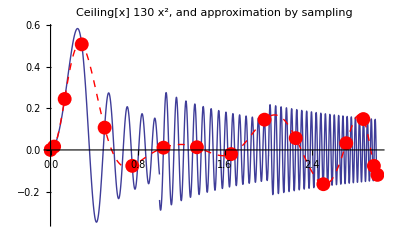

## Mathematica 如何考察输入函数

Mathematica 看到了更深层次的结构

∫_0^3 Ceiling[x] 130 x^2ⅆx

分段函数:

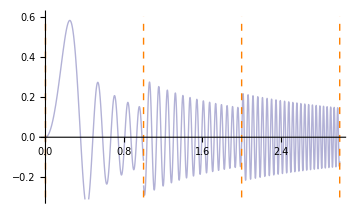
-Graphics-" ⟶ "-Graphics-

特殊积分规则:

-Graphics-" ⟶ "-Graphics-

函数特征:

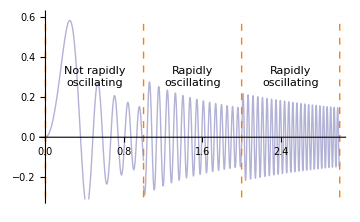
-Graphics-" ⟶ "-Graphics-

可编译的子表达式:

-Graphics-" ⟶ "-Graphics-

上述行为全部自动完成:

```mathematica
NIntegrate[Ceiling[x]BesselJ[1,30x^2],{x,0,3}]
```

0.0859352

方法选择

分类和处理专门领域

-Graphics- | -Graphics- | -Graphics-

方法选择

分类和特殊处理

问题标准化

问题类型分类

高效处理特殊部分

## 问题标准化

找出问题特征并转化成标准形式

```mathematica
NDSolve[{y''[x]+√(4+y''[x])+y[x]==1,y'[0]==0,y[0]==1},y,{x,0,10}]
```

{{y→InterpolatingFunction[{{0.,10.}},<>]},{y→InterpolatingFunction[{{0.,10.}},<>]}}

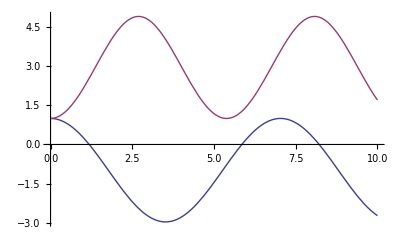

```mathematica
Plot[Evaluate[y[x]/.%],{x,0,10}]
```

NDSolve 把二阶微分方程变成一阶形式:

(∂"")/(∂x) (y(x)
y'(x))==(y'(x)
1/2 (3-√(21-4 y(x))-2 y(x)))
(∂"")/(∂x) (y(x)
y'(x))==(y'(x)
1/2 (3+√(21-4 y(x))-2 y(x)))

## 问题类型分类

NDSolve 可以识别很多类型的方程

偏微分方程:

```mathematica
NDSolve[{D[u[t,x], t]==0.5 D[u[t,x], x,x]+u[t,x] D[u[t,x], x],u[t,-π]==u[t,π]==0,u[0,x]==Sin[x]},u,{t,0,5},{x,-π,π}]
```

{{u→InterpolatingFunction[{{0.,5.},{-3.14159,3.14159}},<>]}}

-Graphics3D-

## 问题类型分类

微分-代数方程

```mathematica
NDSolve[{x'[t]==y[t]^2+x[t] y[t],2 x[t]^2+y[t]^2==1,x[0]==0},{x,y},{t,0,5}]
```

{{x→InterpolatingFunction[{{0.,5.}},<>],y→InterpolatingFunction[{{0.,5.}},<>]}}

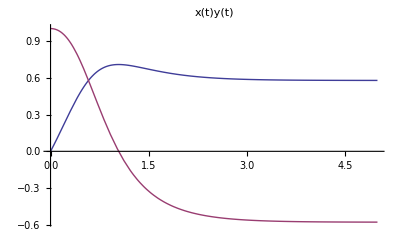

## 问题类型分类

延迟微分方程:

```mathematica
NDSolve[{x'[t]==x[t] (x[t-π]-x'[t-1]),x[t/;t≤0]==Cos[t]},x,{t,0,5}]
```

{{x→InterpolatingFunction[{{0.,5.}},<>]}}

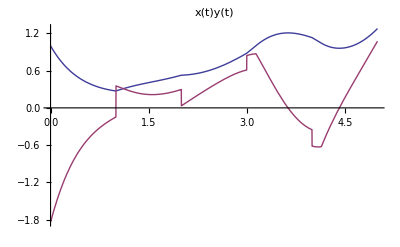

## 问题类型分类

边界值问题:

```mathematica
NDSolve[{x''[t]==y[t] x[t],y'[t]==2-x[t],x[0]==x[4]==1,y[1]==1},{x,y}, t]
```

{{x→InterpolatingFunction[{{0.,4.}},<>],y→InterpolatingFunction[{{0.,4.}},<>]}}

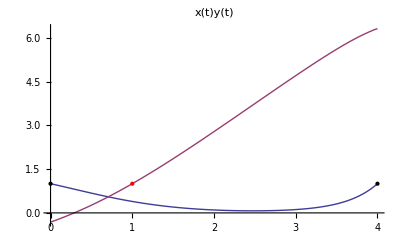

## 高效的针对性算法: 积分

很多针对傅里叶型积分优化的算法:

```mathematica
NIntegrate[10^3 x^(5/2)Cos[10^3 x],{x,0,1}]
```

0.828282

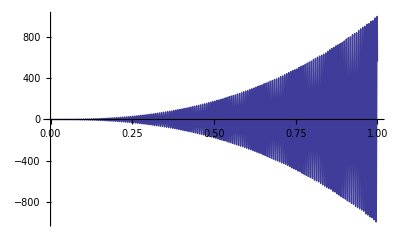

```mathematica
Plot[10^3 x^(5/2)Cos[10^3x],{x,0,1}]
```

通常传统数值方法的耗时很久，结果也不精确:

```mathematica
NIntegrate[10^3 x^(5/2)Cos[10^3 x],{x,0,1},Method->"ClenshawCurtisRule"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.92766}. NIntegrate obtained 0.827938 and 0.00196325 for the integral and error estimates.

0.827938

## 高效的针对性算法: 优化

有约束条件的线性规划:

```mathematica
NMinimize[{5x+y,2x-y/5≥1∧3x+2y≥5},{x,y}]
```

{4.78261,{x→0.652174,y→1.52174}}

或者 (Ver. 12 + )

```mathematica
res=LinearOptimization[5x+y,{2x-y/5≥1,3x+2y≥5},{x,y}]
```

{x→15/23,y→35/23}

```mathematica
N[res]
```

{x→0.652174,y→1.52174}

```mathematica
Show[Plot3D[5x+y,{x,y}∈ImplicitRegion[2x-y/5≥1∧3x+2y≥5,{{x,0,2},{y,0,2}}],],Graphics3D[{Blue,PointSize[0.08],Point[{x,y,5x+y}/. res]}]]
```

-Graphics3D-

混合方法

符号 + 数值的专享能力

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

混合方法

符号 + 数值的专享能力

示例: 分段函数

示例: 建立定制计算方法

## 分段函数: 传统数值计算系统

传统数值对于该类问题仍不能有效解决

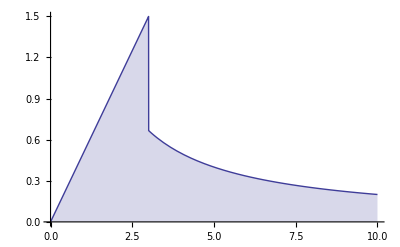

```mathematica
Plot[If[x<3,x/2,2/x],{x,0,10},Filling->Axis]
```

传统方法的取样过程

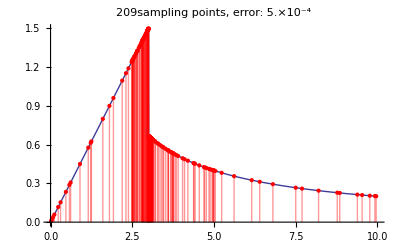

回溯取样顺序

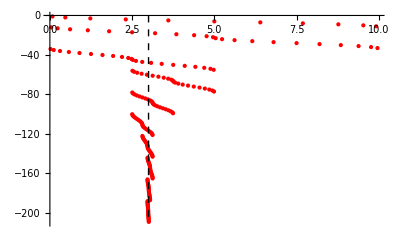

## 分段函数: Mathematica

Mathematica 分析积分因子把它视作 If.

```mathematica
NIntegrate[If[x<3,x/2,2/x],{x,0,10}]
```

4.65795

NIntegrate 取样

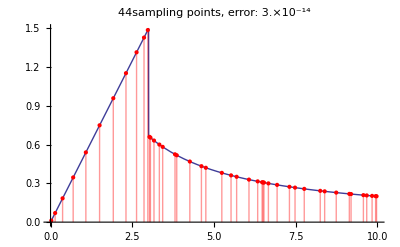

回溯取样过程 NIntegrate:

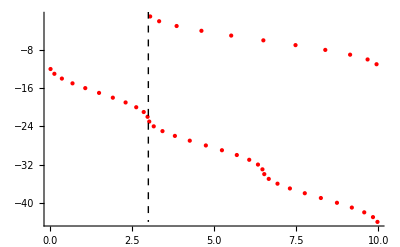

## 分段函数: 深入内部

在函数中任意区域可以分段:

```mathematica
NIntegrate[Sin[Min[(x-1),(x-5)(x-7)]],{x,0,10}]
```

2.16896

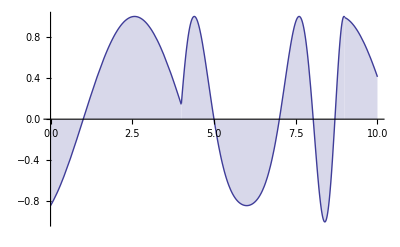

```mathematica
Plot[Sin[Min[(x-1),(x-5)(x-7)]],{x,0,10},Filling->Axis]
```

实际的映射情况:

{x,0,4} | "⟹" | -Sin[1-x]
{x,9,10} | "⟹" | -Sin[1-x]
{x,4,9} | "⟹" | Sin[(-7+x) (-5+x)]

## 分段函数: 深入内部

多变量布尔函数

```mathematica
NIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x](1+Cos[4x y]),{x,-1,1},{y,-1,1}]
```

1.49719

-Graphics3D-

实际映射情况:

{x,-1,-1/(√3)} | {y,-(√(1-x^2))/(√2),(√(1-x^2))/(√2)} | "⟹" | 1+Cos[5 x y]
{x,-1/(√3),-1/2} | {y,x,(√(1-x^2))/(√2)} | "⟹" | 1+Cos[5 x y]
{x,-1/2,-1/(2 √3)} | {y,x,-(√(1-4 x^2))/(2 √2)} | "⟹" | 1+Cos[5 x y]
{x,-1/2,-1/(2 √3)} | {y,(√(1-4 x^2))/(2 √2),(√(1-x^2))/(√2)} | "⟹" | 1+Cos[5 x y]
{x,-1/(2 √3),1/(2 √3)} | {y,(√(1-4 x^2))/(2 √2),(√(1-x^2))/(√2)} | "⟹" | 1+Cos[5 x y]
{x,1/(2 √3),1/(√3)} | {y,x,(√(1-x^2))/(√2)} | "⟹" | 1+Cos[5 x y]
"otherwise" |  | "⟹" | 0

可视化子区间:

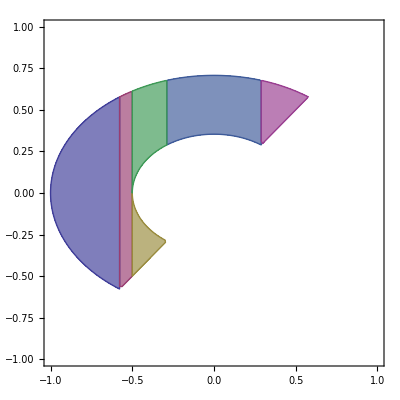

## 建立可定制的计算方法

SIAM 数值计算挑战问题:

∫_0^1 1/x cos((log(x))/x)ⅆx

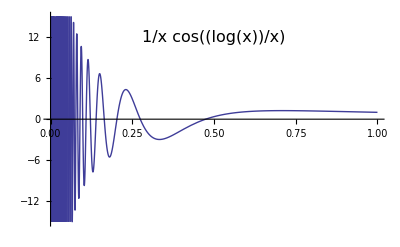

```mathematica
NIntegrate[1/x Cos[Log[x]/x],{x,0,1}]
```

0.323367

Custom oscillatory quadrature rules can be found if a linear ODE can be found.

(∂"")/(∂x) (cos((log(x))/x)
-sin((log(x))/x))==(0 | 1/x^2-(log(x))/x^2
-1/x^2+(log(x))/x^2 | 0).(cos((log(x))/x)
-sin((log(x))/x))

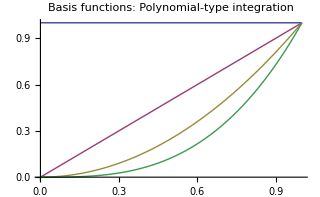
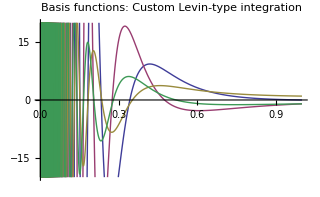

## 建立可定制的计算方法

更为复杂的例子:

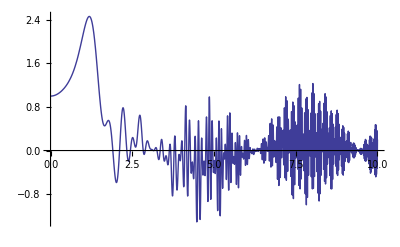

```mathematica
Plot[Sin[x] (Sin[x^2] (Sin[x^3]+1/x)+1/x),{x,0,10}]
```

```mathematica
NIntegrate[Sin[x] (Sin[x^2] (Sin[x^3]+1/x)+1/x),{x,0,∞}]
```

2.43879

手动计算非常繁琐和低效:

(∂"")/(∂x) (sin(x) sin(x^2) sin(x^3)
cos(x^3) sin(x) sin(x^2)
cos(x^2) sin(x) sin(x^3)
cos(x^2) cos(x^3) sin(x)
sin(x) sin(x^2)
cos(x^2) sin(x)
cos(x) sin(x^2) sin(x^3)
cos(x) cos(x^3) sin(x^2)
cos(x) cos(x^2) sin(x^3)
cos(x) cos(x^2) cos(x^3)
cos(x) sin(x^2)
cos(x) cos(x^2)
sin(x)
cos(x))==(0 | 3 x^2 | 2 x | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3 x^2 | 0 | 0 | 2 x | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-2 x | 0 | 0 | 3 x^2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -2 x | -3 x^2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 x | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 x | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 3 x^2 | 2 x | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | -3 x^2 | 0 | 0 | 2 x | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | -2 x | 0 | 0 | 3 x^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | -2 x | -3 x^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 x | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 x | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0).(sin(x) sin(x^2) sin(x^3)
cos(x^3) sin(x) sin(x^2)
cos(x^2) sin(x) sin(x^3)
cos(x^2) cos(x^3) sin(x)
sin(x) sin(x^2)
cos(x^2) sin(x)
cos(x) sin(x^2) sin(x^3)
cos(x) cos(x^3) sin(x^2)
cos(x) cos(x^2) sin(x^3)
cos(x) cos(x^2) cos(x^3)
cos(x) sin(x^2)
cos(x) cos(x^2)
sin(x)
cos(x))

## 建立可定制的计算方法: 内部原理

内部实现方法:

```mathematica
reduction=NIntegrate`LevinIntegrandReduce[Log[x]+FresnelS[√x]/x,x]
```

NIntegrate`LevinIntegrand[3,FresnelS[√x]/x+Log[x],{x},<>]

```mathematica
reduction["Rules"]
```

{Variables→{x},AdditiveTerm→Log[x],Amplitude→{1/x,0,0},Kernel→{FresnelS[√x],Sin[(π x)/2],π √x Cos[(π x)/2]},DifferentialMatrices→{{{0,1/(2 √x),0},{0,0,1/(2 √x)},{0,-1/2 π^2 √x,1/(2 x)}}}}

## 建立可定制的计算方法: 内部原理

强大的内部符号计算能力让混合方法称为可能

```mathematica
DifferentialRootReduce[FresnelS[x],x]
```

DifferentialRoot[Function[{y,x},{x^3 π^2 y'[x]-y''[x]+x y^(3)[x]==0,y[1]==FresnelS[1],y'[1]==1,y''[1]==0}]][x]

## 建立可定制的计算方法: 快速震荡区域检测

sin(x^2-√x) 在 {0,5}是否为快速震荡? {0,50} 上又如何?

定义域为{0, 5}对应的值域:

```mathematica
(x^2-√x)/(2π)/.x->Interval[{0,5.}]
```

Interval[{-0.355881,3.97887}]

定义域为{0, 50}对应的值域:

```mathematica
(x^2-√x)/(2π)/.x->Interval[{0,50.}]
```

Interval[{-1.1254,397.887}]

优化

编译和函数变换

-Graphics- | -Graphics- | -Graphics-

编译

编译和函数变换

编译和表达式优化

求导

函数变换

## 编译和表达式优化

几乎所有数值计算都会自动编译

```mathematica
NDSolve[{y'[t]+Cos[y[t]^2]==y[t]^2,y[0]==1},y,{t,0,1}]
```

{{y→InterpolatingFunction[{{0.,1.}},<>]}}

NDSolve 调用编译过程, 也对通用子表达式进行编译:

```mathematica
Compile[{t,y},y^2-Cos[y^2]]
```

CompiledFunction[{t,y},Block[{Compile`$404},Compile`$404=y^2;Compile`$404-Cos[Compile`$404]],-CompiledCode-]

通用子表达式经常出现 例如一个 Hessian 张量:

```mathematica
D[{Cos[x y],Sin[x y]},{{x,y},2}]
```

{{{-y^2 Cos[x y],-x y Cos[x y]-Sin[x y]},{-x y Cos[x y]-Sin[x y],-x^2 Cos[x y]}},{{-y^2 Sin[x y],Cos[x y]-x y Sin[x y]},{Cos[x y]-x y Sin[x y],-x^2 Sin[x y]}}}

用户无需手动操作:

```mathematica
Compile[{x,y},Evaluate[%]]
```

CompiledFunction[{x,y},Block[{Compile`$434,Compile`$437,Compile`$441,Compile`$442,Compile`$443,Compile`$445,Compile`$421,Compile`$449,Compile`$450,Compile`$446},Compile`$434=x y;Compile`$437=Cos[Compile`$434];Compile`$441=-x y Compile`$437;Compile`$442=Sin[Compile`$434];Compile`$443=-Compile`$442;Compile`$445=Compile`$441+Compile`$443;Compile`$421=y^2;Compile`$449=-x y Compile`$442;Compile`$450=Compile`$437+Compile`$449;Compile`$446=x^2;{{{-Compile`$421 Compile`$437,Compile`$445},{Compile`$445,-Compile`$446 Compile`$437}},{{-Compile`$421 Compile`$442,Compile`$450},{Compile`$450,-Compile`$446 Compile`$442}}}],-CompiledCode-]

## 求导: 最小值

如果知道微分表达式的话，一般数值方法会更有效

```mathematica
FindMinimum[(x-1)^2+2(y-x^2)^2,{x,-1.2},{y,-1}]//Last
```

{x→1.,y→1.}

-Graphics3D-

缺省情况下 准牛顿算法利用了梯度的信息:

```mathematica
D[(x-1)^2+2(y-x^2)^2,{{x,y}}]
```

{2 (-1+x)-8 x (-x^2+y),4 (-x^2+y)}

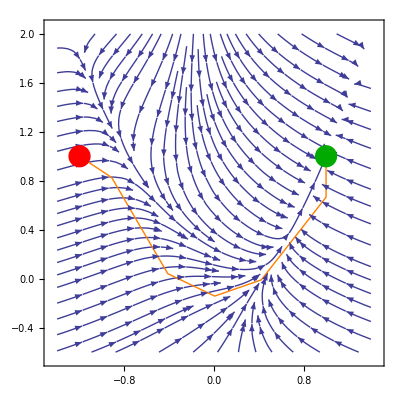

## 求导: 求方程的根

求方程的根用到雅克比矩阵:

```mathematica
FindRoot[{Sin[x+u y],Cos[x-y],u x^2+y^2-z,z+Log[u]},{{x,1},{y,0},{z,0},{u,1}}]
```

{x→0.213568,y→-1.35723,z→1.84925,u→0.157356}

```mathematica
MatrixForm[D[{Sin[x+u y],Cos[x-y],u x^2+y^2-z,z+Log[u]},{{x,y,z,u}}]]
```

(Cos[x+u y] | u Cos[x+u y] | 0 | y Cos[x+u y]
-Sin[x-y] | Sin[x-y] | 0 | 0
2 u x | 2 y | -1 | x^2
0 | 0 | 1 | 1/u)

传统数值方法:

理论情况: 手动写代码并且返回雅克比矩阵

实际情况: 用户一般不做推导，直接使用传统数值系统中的未做优化的方法

Mathematica:

自动求导并且编译

## 函数变换

回顾先前的例子

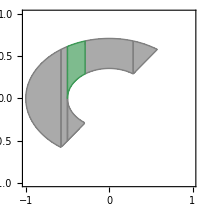
-Graphics3D--Graphics--Graphics3D-

把积分因子转变成一个形态:

| " ⟶ " | -Graphics-
 |  | 
-Graphics3D- | " ⟶ " | -Graphics3D-

结论

智能数值方法选择

特定方法

优化

“I’m so used to mixing numerics and symbolics I generally don’t even think about it.”
		- Darren Glosemeyer, Lead Statistics Developer

## Initialization

Color

```mathematica
Clear[m8red];
m8red[a_]:=RGBColor[0.811765,0.117647,0.145098,a];
```

Packages

```mathematica
Needs["CCodeGenerator`"]
```

```mathematica
Needs["CompiledFunctionTools`"]
```

Special Cells

```mathematica
PicturePrint[expr_,opts:OptionsPattern[Cell]]:=CellPrint[TextCell[expr,"Picture",opts,ShowStringCharacters->False]]
```

```mathematica
OverviewMouseover[header_,subs_]:=CellPrint@Cell[BoxData[ToBoxes@Mouseover[Framed[Style[header,"OverviewSection"],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5],

Evaluate@If[subs=="",Framed[Style[header,"OverviewSection",White],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5,Background->m8red[1]],Row[{Framed[Style[header,"OverviewSection",White],FrameMargins->{{15,15},{5,5}},FrameStyle->None,RoundingRadius->5,Background->m8red[1]]," » ",Framed[Style[subs,"OverviewSection"],FrameMargins->{{15,15},{5,5}},FrameStyle->m8red[1],BoxFrame->2,RoundingRadius->5,Background->White]}]]]],"OverviewSection"]
```

```mathematica
LargeOverviewMouseover[header_,subs_]:=CellPrint@Cell[BoxData[ToBoxes@Mouseover[Framed[Style[header,"LargeOverviewSection"],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5],

Evaluate@If[subs=="",Framed[Style[header,"LargeOverviewSection",White],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5,Background->m8red[1]],Row[{Framed[Style[header,"LargeOverviewSection",White],FrameMargins->{{15,15},{5,5}},FrameStyle->None,RoundingRadius->5,Background->m8red[1]]," » ",Framed[Style[subs,"LargeOverviewSection"],FrameMargins->{{15,15},{5,5}},FrameStyle->m8red[1],BoxFrame->2,RoundingRadius->5,Background->White]}]]]],"LargeOverviewSection"]
```

```mathematica
MapThread[LargeOverviewMouseover,Transpose[{{"Why?","Traditional vs hybrid methods"},{"Method Selection","Classification & specialization"},{"Unique Methods","Made possible with symbolics"},{"Optimization","Compilation & transformations"}}]];
```

## Create custom cells

Utility: CreateSpecialCell

```mathematica
CreateSpecialCell[expr_]:=CellPrint@Cell[BoxData@ToBoxes@expr,"Picture",CellAutoOverwrite->False]
```

```mathematica
CreateSpecialTraditionalFormCell[expr_]:=CellPrint@Cell[BoxData@ToBoxes[expr,TraditionalForm],"Picture",CellAutoOverwrite->False]
```

Utility: LevinODEs

```mathematica
Clear[LevinODEs]
```

```mathematica
LevinODEs[expr_,vars_List]:=TraditionalForm@Column[Block[{li=NIntegrate`LevinIntegrandReduce[expr,vars]},Table[With[{x=vars[[i]],w=MatrixForm@li["Kernel"],A=MatrixForm@Part[li["DifferentialMatrices"],i]},HoldForm[D["",x]w==A.w]],{i,Length[vars]}]],Automatic,1]
```

```mathematica
LevinODEs[expr_,x_]:=LevinODEs[expr,{x}]
```

Utility: FRangesToCube

```mathematica
FRangesToCube[ranges_,cubeSides:{{_,_}...}]:=
Module[{t,t1,jac,vars,rules={}},
vars=First/@ranges;
t=MapThread[(t1=Rescale[#1[[1]],#2,{#1[[2]],#1[[3]]}/.rules];
AppendTo[rules,#1[[1]]->t1];t1)&,{ranges,cubeSides}];
jac=Times@@MapThread[D[#1,#2]&,{t,vars}];
{rules,jac}
]/;Length[ranges]==Length[cubeSides];
FRangesToCube[ranges_,cubeSide:{_,_}]:=FRangesToCube[ranges,Table[cubeSide,{Length[ranges]}]];
FRangesToCube[ranges_]:=FRangesToCube[ranges,{0,1}];
```

NDSolve conversion to first order system

```mathematica
Module[{o=NDSolve`ProcessEquations[{y''[x]+√(4+y''[x])+y[x]==1,y'[0]==0,y[0]==1},y,{x,0,10}]},Style[Column[With[{lhs=MatrixForm@Through[First[o]["DependentVariables"][First@First[o]["IndependentVariables"]]],rhs=MatrixForm[#["NumericalFunction"]["FunctionExpression"][First@First[o]["IndependentVariables"],Sequence@@Through[First[o]["DependentVariables"][First[First[o]["IndependentVariables"]]]]]]},HoldForm[D["",x]lhs==rhs]]&/@o,Spacings->1],Large]]//CreateSpecialTraditionalFormCell
```

NDSolve problem classification

```mathematica
Block[{sol=NDSolve[{D[u[t,x], t]==0.5 D[u[t,x], x,x]+u[t,x] D[u[t,x], x],u[t,-π]==u[t,π]==0,u[0,x]==Sin[x]},u,{t,0,5},{x,-π,π}]},Plot3D[Evaluate[u[t,x]/. First[sol]],{t,0,5},{x,-Pi, Pi}, PlotRange->All,AxesLabel->(Style[#,18]&/@{t,x}),PlotLabel->Style[u[t,x],18]]]//CreateSpecialCell
```

```mathematica
Module[{sol=NDSolve[{x'[t]==y[t]^2+x[t] y[t],2 x[t]^2+y[t]^2==1,x[0]==0},{x,y},{t,0,5}]},Plot[Evaluate[{x[t],y[t]}/.sol],{t,0,5},PlotRange->All,PlotLabel->Row[MapThread[Style[##,18]&,{{x[t],y[t]},ColorData[1]/@Range[2]}],", "]]]//CreateSpecialCell
```

```mathematica
Block[{sol=NDSolve[{x'[t]==x[t] (x[t-π]-x'[t-1]),x[t/;t≤0]==Cos[t]},x,{t,0,5}]},Plot[Evaluate[{x[t],x'[t]} /. First[sol]],{t,0,5}, PlotRange->All,PlotLabel->Row[MapThread[Style[##,18]&,{{x[t],y[t]},ColorData[1]/@Range[2]}],", "]]]//CreateSpecialCell
```

```mathematica
Block[{s=NDSolve[{x''[t]==y[t] x[t],y'[t]==2-x[t],x[0]==x[4]==1,y[1]==1},{x,y}, t]},Plot[Evaluate[{x[t], y[t]} /. First[s]],{t,0,4},Epilog->{PointSize[Large],Point[{0,1}],Point[{4,1}],Red,Point[{1,1}]},PlotLabel->Row[MapThread[Style[##,18]&,{{x[t],y[t]},ColorData[1]/@Range[2]}],", "]]]//CreateSpecialCell
```

NMinimize -> LinearProgramming

```mathematica
Module[{sol=Minimize[{5x+y,2x-y/5>=1∧3x+2y≥5∧x≥0∧y≥0},{x,y}]},Show[Plot3D[5x+y,{x,0,3},{y,0,3},RegionFunction->({x,y,z}↦2x-y/5>1∧3x+2y≥5),AxesLabel->(Style[#,18]&/@{x,y})],Graphics3D[{AbsolutePointSize[10],Red,Point[Append[{x,y}/.Last[sol],First[sol]]]}]]]//CreateSpecialCell
```

What traditional numerical systems see

```mathematica
Style[HoldForm[Integrate[Ceiling[x]BesselJ[1,30x^2],{x,0,3}]],Large]//CreateSpecialTraditionalFormCell
```

```mathematica
With[{int=ImageAdjust[Image[Blur[ImagePad[Rasterize[TraditionalForm@Style[Ceiling[x]BesselJ[1,30x^2],Large]],7,White],10],ImageSize->All],{0,0,1},{0.6,1},{0,1}]},TraditionalForm@Style[HoldForm[Integrate[int,{x,0,3}]],Large]]//CreateSpecialTraditionalFormCell
```

```mathematica
Module[{pts,n=15},pts=Table[{x,Ceiling[x] BesselJ[1,30 x^2]},{x,Sort[Rescale[N@Cos[Range[0,n]/n π],{-1,1},{0,3}]]}];Plot[Evaluate@{Ceiling[x]BesselJ[1,30x^2],InterpolatingPolynomial[pts,x]},{x,0,3},PlotPoints->200,Epilog->{PointSize[0.025],Red,Point[pts]},PlotStyle->{Automatic,Directive[Thick,Red,Dashed]},PlotLabel->Row[{Style[Ceiling[x] BesselJ[1,30 x^2],14,ColorData[1][1]],Style[", and approximation by ",14],Style["sampling",14,Lighter@Red]}]]]//CreateSpecialCell
```

What Mathematica sees

```mathematica
Style[HoldForm[Integrate[Ceiling[x]BesselJ[1,30x^2],{x,0,3}]],Large]//CreateSpecialTraditionalFormCell
```

```mathematica
Row[{Module[{frame,doframes},
SetAttributes[doframes,HoldAll];
doframes[expr_]:=HoldForm[expr]/.frame[e_]:>Framed[e,RoundingRadius->5,Background->Directive[Opacity[0.4],Orange],FrameStyle->Directive[Orange]];Image[Rasterize[TraditionalForm@Style[doframes[Integrate[frame[Ceiling[x]]BesselJ[1,30x^2],{x,0,3}]],Large]],ImageSize->All]],Framed[Style[" ⟶ ",Bold,36,Orange],FrameStyle->None],Plot[Ceiling[x]BesselJ[1,30x^2],{x,0,3},PlotPoints->200,PlotStyle->Opacity[0.4],PlotRange->{-0.31,0.61},ImageSize->Medium,Epilog->{Thick,Orange,Dashed,Line[{{#,-0.3},{#,0.6}}]&/@Range[0,3]}]}]//CreateSpecialCell
```

```mathematica
Row[{Module[{frame,doframes},
SetAttributes[doframes,HoldAll];
doframes[expr_]:=HoldForm[expr]/.frame[e_]:>Framed[e,RoundingRadius->5,Background->Directive[Opacity[0.4],Purple],FrameStyle->Directive[Purple]];Image[Rasterize[TraditionalForm@Style[doframes[Integrate[Ceiling[x]frame@BesselJ[1,30x^2],{x,0,3}]],Large]],ImageSize->All]],Framed[Style[" ⟶ ",Bold,36,Purple],FrameStyle->None],Image[Rasterize@TraditionalForm[Style[First[First[Head[DifferentialRootReduce[BesselJ[1,30x^2],x]]][y,x]],Large,Purple]],ImageSize->All]}]//CreateSpecialCell
```

```mathematica
Grid[{{Module[{frame,doframes},
SetAttributes[doframes,HoldAll];
doframes[expr_]:=HoldForm[expr]/.frame[e_]:>Framed[e,RoundingRadius->5,Background->Directive[Opacity[0.4],Purple],FrameStyle->Directive[Purple]];Image[Rasterize[TraditionalForm@Style[doframes[Integrate[Ceiling[x]frame@BesselJ[1,30x^2],{x,0,3}]],Large]],ImageSize->All]],Framed[Style[" ⟶ ",Bold,36,Purple],FrameStyle->None],Image[Rasterize@TraditionalForm[Style[First[First[Head[DifferentialRootReduce[BesselJ[1,30x^2],x]]][y,x]],Large,Purple]],ImageSize->All]},{"",Framed[Style[" ⟶ ",Bold,36,Purple],FrameStyle->None],Item[Image[Rasterize@StandardForm[Text@Style["Custom integration rule ...",Large,Purple]],ImageSize->All],Alignment->Left]}}]//CreateSpecialCell
```

```mathematica
Row[{Module[{frame,doframes},
SetAttributes[doframes,HoldAll];
doframes[expr_]:=HoldForm[expr]/.frame[e_]:>Framed[e,RoundingRadius->5,Background->Directive[Opacity[0.4],Lighter@Blue],FrameStyle->Directive[Blue]];Image[Rasterize[TraditionalForm@Style[doframes[Integrate[Ceiling[x]BesselJ[1,frame[30x^2]],{x,0,3}]],Large]],ImageSize->All]],Framed[Style[" ⟶ ",Bold,36,Lighter@Blue],FrameStyle->None],Plot[Ceiling[x]BesselJ[1,30x^2],{x,0,3},PlotPoints->200,PlotStyle->Opacity[0.4],PlotRange->{-0.31,0.61},ImageSize->Medium,Epilog->{{FaceForm[Directive[Opacity[0.0],Lighter@Blue]],EdgeForm[None],Rectangle[{1,-0.3},{2,0.6}],Rectangle[{2,-0.3},{3,0.6}]},{Inset[Framed[#,RoundingRadius->5,Background->Directive[Opacity[0.4],Lighter@Gray],FrameStyle->Directive[Gray]]&@Style["Not rapidly\noscillating",16,Black],{0.5,0.3}],Inset[Framed[#,RoundingRadius->5,Background->Directive[Opacity[0.4],Lighter@Blue],FrameStyle->Directive[Blue]]&@Style["Rapidly\noscillating",16,Black],{1.5,0.3}],Inset[Framed[#,RoundingRadius->5,Background->Directive[Opacity[0.4],Lighter@Blue],FrameStyle->Directive[Blue]]&@Style["Rapidly\noscillating",16,Black],{2.5,0.3}]},{Thick,Orange,Dashed,Line[{{#,-0.3},{#,0.6}}]&/@Range[0,3]}}]}]//CreateSpecialCell
```

```mathematica
Row[{Module[{frame,doframes},
SetAttributes[doframes,HoldAll];
doframes[expr_]:=HoldForm[expr]/.frame[e_]:>Framed[e,RoundingRadius->5,Background->Directive[Opacity[0.4],Darker@Green],FrameStyle->Directive[Darker@Green]];Image[Rasterize[TraditionalForm@Style[doframes[Integrate[frame[Ceiling[x]]BesselJ[1,frame[30x^2]],{x,0,3}]],Large]],ImageSize->All]],Framed[Style[" ⟶ ",Bold,36,Darker@Green],FrameStyle->None],Image[Rasterize@StandardForm[Style[HoldForm[CompiledFunction[…]],Large,Bold,Darker@Green]],ImageSize->All]}]//CreateSpecialCell
```

Piecewise integration: Traditional

```mathematica
Module[{res,exact,pts},
exact=Integrate[If[x<3,x/2,2/x],{x,0,10}];pts=Last[Last[Reap[res=Quiet@NIntegrate[If[x<3,x/2,2/x],{x,0,10},EvaluationMonitor:>Sow[{x,If[x<3,x/2,2/x]}],Method->{Automatic,"SymbolicProcessing"->None}]]]];Show[Plot[If[x<3,x/2,2/x],{x,0,10},PlotLabel->Style[Row[{Length[pts],"sampling points, error: ",ScientificForm[Abs[exact-res],1]}," "],18]],ListPlot[pts,Filling->Axis,PlotStyle->Red,FillingStyle->Directive[Opacity[0.4],Red]]]]//CreateSpecialCell
```

```mathematica
Module[{exact,pts},pts=Last[Last[Reap[Quiet@NIntegrate[If[x<3,x/2,2/x],{x,0,10},EvaluationMonitor:>Sow[{x,If[x<3,x/2,2/x]}],Method->{Automatic,"SymbolicProcessing"->None}]]]];ListPlot[Thread[{First/@pts,-Range[Length[pts]]}],Axes->{True,False},PlotRange->All,PlotStyle->Red,Epilog->{Black,Dashed,Line[{{3,0},{3,-Length[pts]}}]}]]//CreateSpecialCell
```

Piecewise integration: NIntegrate

```mathematica
Module[{res,exact,pts},
exact=Integrate[If[x<3,x/2,2/x],{x,0,10}];pts=Last[Last[Reap[res=Quiet@NIntegrate[If[x<3,x/2,2/x],{x,0,10},EvaluationMonitor:>Sow[{x,If[x<3,x/2,2/x]}]]]]];Show[Plot[If[x<3,x/2,2/x],{x,0,10},PlotLabel->Style[Row[{Length[pts],"sampling points, error: ",ScientificForm[Abs[exact-res],1]}," "],18]],ListPlot[pts,Filling->Axis,PlotStyle->Red,FillingStyle->Directive[Opacity[0.4],Red]]]]//CreateSpecialCell
```

```mathematica
Module[{exact,pts},pts=Last[Last[Reap[Quiet@NIntegrate[If[x<3,x/2,2/x],{x,0,10},EvaluationMonitor:>Sow[{x,If[x<3,x/2,2/x]}]]]]];ListPlot[Thread[{First/@pts,-Range[Length[pts]]}],Axes->{True,False},PlotRange->All,PlotStyle->Red,Epilog->{Black,Dashed,Line[{{3,0},{3,-Length[pts]}}]}]]//CreateSpecialCell
```

Piecewise integration: NIntegrate under the hood

```mathematica
Style[Grid[Insert[#,"⟹",2]&/@Reverse/@Simplify`PiecewiseNIntegrate[Sin[Min[(x-1),(x-5)(x-7)]],{{x,0,10}},{},{}],Alignment->Left],Large]//CreateSpecialCell
```

Piecewise integration: NIntegrate multidimensional with Boole

```mathematica
Plot3D[1+Cos[4x y],{x,-1,1},{y,-1,1},RegionFunction->({x,y}↦1/4≤x^2+2y^2≤1∧y>x),Filling->0,PlotRange->{0,All},Mesh->None,PlotLabel->Style[1+Cos[4x y],16]]//CreateSpecialCell
```

```mathematica
Style[Grid[Insert[#,"⟹",3]&/@Append[RotateLeft/@Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x](1+Cos[5x y]),{{x,-1,1},{y,-1,1}},{},{}],{Item[Text@"otherwise",Alignment->Center],SpanFromLeft,0}],Alignment->Left],18]//CreateSpecialCell
```

```mathematica
Show[MapIndexed[RegionPlot[Tooltip[#,TraditionalForm@#],{x,-1,1},{y,-1,1},PlotPoints->65,BoundaryStyle->ColorData[1][#2[[1]]],PlotStyle->Lighter[ColorData[1][#2[[1]]]]]&,And@@@Map[#[[2]]<#[[1]]<#[[3]]&,Take[#,-2]&/@Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x](1+Cos[5x y]),{{x,-1,1},{y,-1,1}},{},{}],{2}]]]//CreateSpecialCell
```

LevinRule

```mathematica
Style[HoldForm[Integrate[HoldForm[1/x]Cos[Log[x]/x],{x,0,1}]],Large]//CreateSpecialTraditionalFormCell
```

```mathematica
Plot[1/x Cos[Log[x]/x],{x,0,1},PlotRange->15,Epilog->Inset[Style[HoldForm[1/x]Cos[Log[x]/x],16],{0.5,12}]]//CreateSpecialCell
```

```mathematica
TraditionalForm[Style[LevinODEs[1/x Cos[Log[x]/x],x],Large]]//CreateSpecialTraditionalFormCell
```

```mathematica
Row[{Plot[Evaluate[x^Range[0,3]],{x,0,1},ImageSize->320,PlotLabel->Style["Basis functions: Polynomial-type integration",16]],Spacer[10],Plot[Evaluate@Module[{li=NIntegrate`LevinIntegrandReduce[1/x Cos[Log[x]/x],x]},li["LevinBasis"[2]].li["Kernel"]],{x,0,1},PlotRange->20,ImageSize->320,PlotLabel->Style["Basis functions: Custom Levin-type integration",16]]},Spacer[10]]//CreateSpecialCell
```

```mathematica
TraditionalForm[Style[LevinODEs[Sin[x] (Sin[x^2] (Sin[x^3]+1/x)+1/x),x],13]]//CreateSpecialTraditionalFormCell
```

Optimization: Derivatives in minimization

```mathematica
Module[{f,pts},f[x_,y_]:=(x-1)^2+2(y-x^2)^2;pts=Last[Last[Reap[Sow[{-1.2,1,f[-1.2,1]}];FindMinimum[f[x,y],{{x,-1.2},{y,1}},StepMonitor:>Sow[{x,y,f[x,y]}]]]]];Show[Plot3D[f[x,y],{x,-1.4,1.4},{y,-0.6,2},Mesh->5,PlotStyle->Automatic,PlotLabel->Style[Row[{"Steps while minimizing  ",(x-1)^2+2(y-x^2)^2}],16]],Graphics3D[{Orange,PointSize[0.025],Point[Rest[Most[pts]]],Thick,Line[pts],Darker@Green,PointSize[0.05],Point[Last[pts]],Red,Point[First[pts]]}]]]//CreateSpecialCell
```

```mathematica
Module[{f,pts},f[x_,y_]:=(x-1)^2+2(y-x^2)^2;pts=Last[Last[Reap[Sow[{-1.2,1,f[-1.2,1]}];FindMinimum[f[x,y],{{x,-1.2},{y,1}},StepMonitor:>Sow[{x,y,f[x,y]}]]]]];StreamPlot[Evaluate[-D[(x-1)^2+2(y-x^2)^2,{{x,y}}]],{x,-1.4,1.4},{y,-0.6,2},Epilog->{Thick,Orange,Line[Most/@pts],PointSize[0.04],Darker@Green,Point[{1,1}],Red,Point[{-1.2,1}]},StreamStyle->Arrowheads[0.025]]]//CreateSpecialCell
```

Optimization: NIntegrate UnitCubeRescaling

```mathematica
Module[{w=255,view={ViewPoint->{-0.0061646510098131,-1.3198910258802454,3.115742235307458},ViewCenter->{0.5,0.5,0.5},ViewVertical->{0.,0.,1.}}},Row[{
Plot3D[1+Cos[4x y],{x,-1,1},{y,-1,1},RegionFunction->({x,y}↦1/4≤x^2+2y^2≤1∧y>x),Filling->0,PlotRange->{0,All},Mesh->None,Evaluate[view],ImageSize->w],
Show[MapIndexed[RegionPlot[Tooltip[#,TraditionalForm@#],{x,-1,1},{y,-1,1},PlotPoints->65,BoundaryStyle->If[#2[[1]]==4,ColorData[1][4],Gray],PlotStyle->Lighter@If[#2[[1]]==4,ColorData[1][4],Gray]]&,And@@@Map[#[[2]]<#[[1]]<#[[3]]&,Take[#,-2]&/@Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x](1+Cos[5x y]),{{x,-1,1},{y,-1,1}},{},{}],{2}]],ImageSize->0.8w],
Plot3D[1+Cos[4x y],{x,-0.7,0.0},{y,0,0.7},RegionFunction->({x,y}↦Evaluate[Part[And@@@Map[#[[2]]<#[[1]]<#[[3]]&,Take[#,-2]&/@Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x](1+Cos[5x y]),{{x,-1,1},{y,-1,1}},{},{}],{2}],4]]),Filling->0,PlotRange->{1,All},Mesh->5,Evaluate[view],ImageSize->w]},Spacer[8]]]//CreateSpecialCell
```

```mathematica
Grid[{{Rasterize[TraditionalForm[Style[1+Cos[5x y],Large]]],Framed[Style[" ⟶ ",Bold,36,Black],FrameStyle->None],Rasterize[TraditionalForm[Pane[Style[Simplify[Module[{transRules,jacobian,f},
f[x_,y_]:=(1+Cos[5x y]);{transRules,jacobian}=FRangesToCube[Rest[Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x]f[x,y],{{x,-1,1},{y,-1,1}},{},{}][[4]]]];(f[x,y]/.transRules)jacobian],0<x<1&&0<y<1],Small],400]]]},{Spacer[{5,5}],SpanFromLeft,SpanFromLeft},{Plot3D[1+Cos[4x y],{x,-0.7,0.0},{y,0,0.7},RegionFunction->({x,y}↦Evaluate[Part[And@@@Map[#[[2]]<#[[1]]<#[[3]]&,Take[#,-2]&/@Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x](1+Cos[5x y]),{{x,-1,1},{y,-1,1}},{},{}],{2}],4]]),Filling->0,PlotRange->{1,All},Mesh->5,PlotLabel->Style[Row[{"Integral: ",NIntegrate@@Part[Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x](1+Cos[5x y]),{{x,-1,1},{y,-1,1}},{},{}],4]}],14],{ViewPoint->{-0.0061646510098131,-1.3198910258802454,3.115742235307458},ViewCenter->{0.5,0.5,0.5},ViewVertical->{0.,0.,1.}},ImageSize->250],Framed[Style[" ⟶ ",Bold,36,Black],FrameStyle->None],Module[{g=Simplify[Module[{transRules,jacobian,f},
f[x_,y_]:=(1+Cos[5x y]);{transRules,jacobian}=FRangesToCube[Rest[Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x]f[x,y],{{x,-1,1},{y,-1,1}},{},{}][[4]]]];(f[x,y]/.transRules)jacobian],0<x<1&&0<y<1]},Show[Plot3D[g,{x,0,1},{y,0,1},Filling->Axis,Mesh->5,PlotRange->{0,All},PlotPoints->50,ImageSize->250,{ViewPoint->{-0.0061646510098131,-1.3198910258802454,3.115742235307458},ViewCenter->{0.5,0.5,0.5},ViewVertical->{0.,0.,1.}},PlotLabel->Style[Row[{"Integral: ",NIntegrate@@Part[Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x](1+Cos[5x y]),{{x,-1,1},{y,-1,1}},{},{}],4]}],14],PlotStyle->Opacity[0.75]],Graphics3D[{PointSize[0.03],Black,Point[Append[#,g/.Thread[{x,y}->#]]&/@Module[{numberOfGenerators,dimension,precision,rdata,generators,weights,pts},
numberOfGenerators=9;
MakeOrbit[generator_]:=
Module[{perms,signs,gperms,len=Length[generator]},
perms=Permutations[Range[len]];
signs=Flatten[Outer[List,Sequence@@Table[{1,-1},{len}]],len-1];
gperms=Map[Part[generator,#1]&,perms];
Union[Flatten[Outer[Times,gperms,signs,1],1]]
];
dimension=2;
precision=MachinePrecision;
rdata=NIntegrate`MultiDimensionalRuleData[numberOfGenerators,precision,dimension];
generators=rdata[[1,1]];
weights=rdata[[1,2]];
pts=Flatten[MakeOrbit/@generators,1]+0.5
]]}]]]}}]//CreateSpecialCell
```

Unused

```mathematica
Show[Part[MapIndexed[RegionPlot[Tooltip[#,TraditionalForm@#],{x,-0.7,0.0},{y,0,0.7},PlotPoints->65,BoundaryStyle->ColorData[1][#2[[1]]],PlotStyle->Lighter[ColorData[1][#2[[1]]]]]&,And@@@Map[#[[2]]<#[[1]]<#[[3]]&,Take[#,-2]&/@Simplify`PiecewiseNIntegrate[Boole[1/4≤x^2+2y^2≤1∧y>x](1+Cos[5x y]),{{x,-1,1},{y,-1,1}},{},{}],{2}]],4]]//CreateSpecialCell
```

## Create chapter graphics

Utility: CreatePictureRowCell

```mathematica
CreatePictureGridCell[exprs_List,height_]:=CreateSpecialCell[Style[Grid[Map[Image[ImageResize[#,{Automatic,height}],ImageSize->All]&,exprs,{2}],Spacings->{1,1}]]]
```

Why

```mathematica
CreatePictureGridCell[{{Module[{pts,n=15},pts=Table[{x,Ceiling[x] BesselJ[1,30 x^2]},{x,Sort[Rescale[N@Cos[Range[0,n]/n π],{-1,1},{0,3}]]}];Plot[Evaluate@{Ceiling[x]BesselJ[1,30x^2],InterpolatingPolynomial[pts,x]},{x,0,3},PlotPoints->200,Epilog->{PointSize[0.025],Red,Point[pts]},PlotStyle->{Automatic,Directive[Thick,Red,Dashed]}]],-Graphics-}},200]
```

Method Selection

```mathematica
CreatePictureGridCell[{{-Graphics3D-,-Graphics-,-Graphics-}},150]
```

Unique Methods

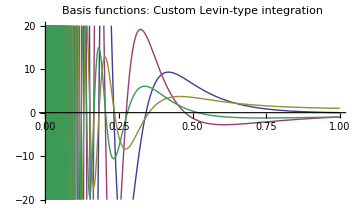
```mathematica
CreatePictureGridCell[{{-Graphics-,-Graphics-,-Graphics-},{-Graphics3D-,-Graphics-,-Graphics-}},150]
```

Optimization

```mathematica
CreatePictureGridCell[{{-Graphics-,-Graphics3D-,-Graphics3D-}},200]
```

## Lastly

```mathematica
$Line=0;
```